```mathematica
utt354 =Import["~/workspace/gnu-radio/recordings/3_5_4.wav"]
```

-Graphics-

## Given two vectors we want a formula for the delta vector between them

```mathematica
ListSeriesDelta[twosome_] := Table[twosome[[2,i]]-twosome[[1,i]], {i, 1, Length[twosome[[1]]]}]
```

```mathematica
test = {{1,2,3,4,5},{3,4,5,6,7}}
```

{{1,2,3,4,5},{3,4,5,6,7}}
 |  |  |  |

```mathematica
ListSeriesDelta[test]
```

{2,2,2,2,2}

## A formular that Partitions and deltas a list in one go

the formular partitions the list given as the first parameter into sub-lists whose size is the second parameter. It then takes pairs of these sublists and s them to one list of deltas between the sublists.

```mathematica
PartitionAndDeltaList = Flatten[#]& @ Map[ListSeriesDelta, #]& @ Partition[#,2]& @ Partition[#,#2]&
```

(((Flatten[#1]&)[ListSeriesDelta/@#1]&)[Partition[#1,2]]&)[Partition[#1,#2]]&
 |  |  |  |

```mathematica
PartitionAndDeltaList [{1,2,3,4,5,6,7,8,9},3]
```

{3,3,3}

need to
- determine the 13 mell bank ranges of the sample windows from the highest resolution window 
- determine how to detect that deltas are below noise (e.g. magnitude is way below that of signal at the sample window wavelength)
- what to do with outlier deltas... maybe apply correction and keep that as a prediction for the next window. If the prediction holds for a while we may have a new symbol
- what to do when deltas are haphazardly different? consider double delta? Maybe consider the larger window delta as this may imply a groundswell?
- when if ever are double deltas useful?
- For larger windows we need to reduce the deltas to the same number of points as the highest resolution window. Can do this using the NestWhiling of the ReducePartitionDelta function in the asr-research-more notebook?

## A formular to determine binary vector features using thresholds on list of deltas

```mathematica
d4 = PartitionAndDeltaList[utt354[[1,1,1]], 4]
```

{-0.00643921,-0.00717163,0.00271606,-0.00292969,0.0043335,-0.00372314,0.00460815,0.015686,110232,-0.000457764,0.0103149,0.00192261,-0.00521851,0.000305176,0.00106812,0.00817871,-0.000854492}
 |  |  |  |

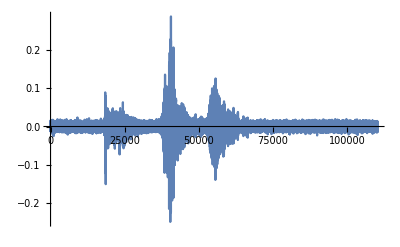

```mathematica
ListLinePlot[d4, PlotRange->All]
```

```mathematica
AboveThreshold[list_] := Count[list, u_/;Abs[u]>0.05] >4
```

```mathematica
Count[#, u_/;Abs[u]>0.002]& @ {1,2,3,4}
```

4

```mathematica
AboveThreshold[{0,1,2,3,4}]
```

False

```mathematica
d4Filtered = Map[If[AboveThreshold[#],#,{0,0,0,0,0,0,0,0}]&, Partition[utt354[[1,1,1]],8]]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},27546,{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}
 |  |  |  |

```mathematica
ListLinePlot[Flatten[d4Filtered], PlotRange -> All]
```

-Graphics-

```mathematica
newS = Sound[SampledSoundList[Flatten[d4Filtered],44100]]
```

-Graphics-

```mathematica
fred = Play[(2+Cos[50 t])*Sin[2000*(1+ Round[2t,0.1])* t] , {t,0,1}]
```

-Graphics-

```mathematica
fred
```

-Graphics-

## Compose the functions to synthesize the feature data

Need to compose the
- ListSeriesDelta function
- Partition Function
- Threshold function to obtain 1’s and 0’s 
-- consume a flattened list of deltas
-- Output 1 in corresponding slot if delta exeeds threshold
-- Decensitizes by moving threshold up  for a given number of samples after detecting a 1 then returns it back
- Hamming distance function to detect symbols/signal/order in the corresponding binary vector